```mathematica
Clear[x,y]
```

```mathematica
L=2;
W=1;
x=1;
y=0.5;
T1=50;
T2=150;
Do[Print[{(2 ((-1)^(n+1)+1) Sin[(π n x)/L] Sinh[(π n y)/L])/(π n Sinh[(π n W)/L])}],{n,1,9}]
THETA=∑_(n=1)^5 {(2 ((-1)^(n+1)+1) Sin[(π n x)/L] Sinh[(π n y)/L])/(π n Sinh[(π n W)/L])}
T=THETA (T2-T1)+T1
```

{0.48061}

{0.}

{-0.0398678}

{0.}

{0.00501535}

{0.}

{-0.000744983}

{0.}

{0.000120454}

{0.445757}

{94.5757}

-Graphics3D-

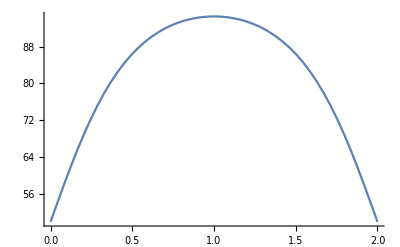

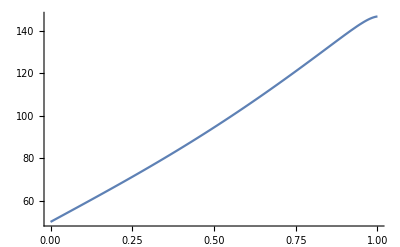

{{θ[x,y]→InterpolatingFunction[{{0., 2.}, {0., 1.}}, <>][x,y]}}

-Graphics3D-

```mathematica
L = 2;
W=1;
Plot3D[T1+(T2-T1)*2/π*Sum[{(((-1)^(n+1)+1)/n)Sin[n*π*x/L]*Sinh[n*π*y/L]/Sinh[n*π*W/L]}
,{n,1,20}],{x,0,L},{y,0,W}]

Clear [x]
y=0.5;
Plot[T1+(T2-T1)*2/π*Sum[{(((-1)^(n+1)+1)/n)Sin[n*π*x/L]*Sinh[n*π*y/L]/Sinh[n*π*W/L]}
,{n,1,20}],{x,0,L}]

Clear[y]
x=1;
Plot[T1+(T2-T1)*2/π*Sum[{(((-1)^(n+1)+1)/n)Sin[n*π*x/L]*Sinh[n*π*y/L]/Sinh[n*π*W/L]}
,{n,1,20}],{y,0,W}]

Clear[θ,x,y]
NDSolve[{D[θ[x,y],{x,2}]+ D[θ[x,y],{y,2}]==0,θ[0,y]==0,θ[2,y]==0,θ[x,1]==1,θ[x,0]==0},θ[x,y],{x,0,2},{y,0,1}]
Plot3D[Evaluate[θ[x,y] /.%],{x,0,2},{y,0,1},PlotRange->All]
```

```mathematica
k=1;
L = 2;
W=1;

Clear [THETA];
Clear[x];
Clear [y];
A=1;

THETA[x_,y_]=Sum[{2/π*(((-1)^(n+1)+1)/n)Sin[n*π*x/L]*Sinh[n*π*y/L]/Sinh[n*π*W/L]}
,{n,1,9}]

THETA[0.5,0.5]
```

{(4 Csch[π/2] Sin[(π x)/2] Sinh[(π y)/2])/π+(4 Csch[(3 π)/2] Sin[(3 π x)/2] Sinh[(3 π y)/2])/(3 π)+(4 Csch[(5 π)/2] Sin[(5 π x)/2] Sinh[(5 π y)/2])/(5 π)+(4 Csch[(7 π)/2] Sin[(7 π x)/2] Sinh[(7 π y)/2])/(7 π)+(4 Csch[(9 π)/2] Sin[(9 π x)/2] Sinh[(9 π y)/2])/(9 π)}

{0.364045}

```mathematica
DTHETA[x_,y_]=D[{(4 Csch[π/2] Sin[(π x)/2] Sinh[(π y)/2])/π+(4 Csch[(3 π)/2] Sin[(3 π x)/2] Sinh[(3 π y)/2])/(3 π)+(4 Csch[(5 π)/2] Sin[(5 π x)/2] Sinh[(5 π y)/2])/(5 π)+(4 Csch[(7 π)/2] Sin[(7 π x)/2] Sinh[(7 π y)/2])/(7 π)+(4 Csch[(9 π)/2] Sin[(9 π x)/2] Sinh[(9 π y)/2])/(9 π)},y]
```

{2 Cosh[(π y)/2] Csch[π/2] Sin[(π x)/2]+2 Cosh[(3 π y)/2] Csch[(3 π)/2] Sin[(3 π x)/2]+2 Cosh[(5 π y)/2] Csch[(5 π)/2] Sin[(5 π x)/2]+2 Cosh[(7 π y)/2] Csch[(7 π)/2] Sin[(7 π x)/2]+2 Cosh[(9 π y)/2] Csch[(9 π)/2] Sin[(9 π x)/2]}

```mathematica
L=2;
k=50;
T2=150;
T1=50;

y=0;
NIntegrate[k*(T2-T1)*{2 Cosh[(π y)/2] Csch[π/2] Sin[(π x)/2]+2 Cosh[(3 π y)/2] Csch[(3 π)/2] Sin[(3 π x)/2]+2 Cosh[(5 π y)/2] Csch[(5 π)/2] Sin[(5 π x)/2]+2 Cosh[(7 π y)/2] Csch[(7 π)/2] Sin[(7 π x)/2]+2 Cosh[(9 π y)/2] Csch[(9 π)/2] Sin[(9 π x)/2]},{x,0,L}]
```

{8346.27}

```mathematica
L=2;
k=50;
T2=150;
T1=50;

y=0;

y=0;
NIntegrate[k*(T2-T1)*DTHETA[x_,y],{x,0,L}]
```

{8346.27}